OpenMATLAB::wspo: The MATLAB workspace is already open.

{{G1→1.28844×10^-7,G2→1.3512×10^-7,G3→2.78734×10^-6,P2→0.0000146139,P3→0.000301464,G4→1.28844×10^-7,G5→1.28844×10^-7,P1→0.0000139351,P4→0.0000139351,P5→0.0000139351,M3→36.4385,M2→29.8691,M1→32.5232},{G1→1.28844×10^-7,G2→4.1367×10^-7,G3→4.1367×10^-7,P2→0.0000447404,P3→0.0000447404,G4→1.28844×10^-7,G5→1.28844×10^-7,P1→0.0000139351,P4→0.0000139351,P5→0.0000139351,M3→36.6501,M2→30.3256,M1→31.8437}}

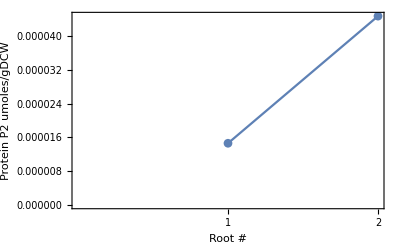

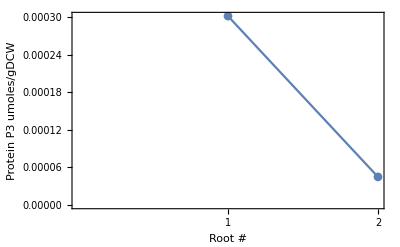

```mathematica
Needs["MATLink`"];
ClearAll["Global`*"];
OpenMATLAB[];
MEvaluate["feature('DefaultCharacterSet','windows-1252');"];
MFunction["cd"]["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\Kinetic Model"];
modelgen= MFunction["gen_model"];	
model=modelgen["C:\\Users\\shyam\\SkyDrive\\Documents\\Courses\\Modeling Project\\TRN Model\\TRNtest8.txt"];
Vicind=IntegerPart["Vic_exind"/.model];
Vxcind=IntegerPart["Vxc_exind"/.model];
bmind=IntegerPart["bm_ind"/.model];
fluxind:=MFunction["fluxind","OutputArguments"->4];
S=Normal["S"/.model];
{vuptake,vexcrt,intind,exind}=fluxind[Vicind,Vxcind,S];
(*CloseMATLAB[];
DisconnectEngine[];*)

metint={M1,M2,M3};
metext={M1xt,M2xt};
protein={P1,P2,P3,P4,P5};
genes={G1,G2,G3,G4,G5};
trate={G1->P1,G2->P2,G3->P3,G4->P4,G5->P5};
fluxes={vuptake,v1,v2,v3,vexcrt,mu};
mu=0.2/3600;(*s-1*)
vuptake=0.00556;
alpha=40/(233/(mu*3600)^2+78);
beta=60/(82.5/(mu*3600)+148);
RNAP=3*^-5;(*uM*)
(*Gene Reactions*)
gdecay=0.0031;
pdecay=3.83*^-6;
G1prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate+alphac*0)
		];
G2prod:=Block[{brate=500,alphac=0.06,Kp3=1*^-6},
			RNAP*((alpha/brate)+alphac*1/(1+(P3/Kp3)^2))
		];                                                                                                                                                                      
G3prod:=Block[{brate=500,alphac=0.06,Kp2=1*^-6},
			RNAP*(alpha/brate+alphac*1/(1+(P2/Kp2)^2))
		];
G4prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate+alphac*0)
		];
G5prod:=Block[{brate=500,alphac=0.06},
			RNAP*(alpha/brate+alphac*0)
		];
gReactions:=Table[rg[i],{i,1,5}];

rg[1]:=G1prod-(gdecay+mu)*G1;
rg[2]:=G2prod-(gdecay+mu)*G2;
rg[3]:=G3prod-(gdecay+mu)*G3;
rg[4]:=G4prod-(gdecay+mu)*G4;
rg[5]:=G5prod-(gdecay+mu)*G5;
(*Protein Reactions*)
SetAttributes[translation,Listable];
translation[gp_]:=Module[{list=gp,gprod,G,P},
				G=Keys[list];
				P=Values[list];
				gprod=0.06*beta*G-(pdecay+mu)*P
				];
pReactions:=Table[translation[trate[[i]]],{i,1,5}];
(*Metabolite Reactions*)
mReactions:=Table[rm[i],{i,1,3}];
flux[sub_,prod_,spar_,ppar_,eqp_]:=Module[{S=sub,P=prod,Ks=spar,Kp=ppar,Keq=eqp,
											piP,piS,dS,dP,piSs,piPs,Vt,Vs,Vr,
											V},
	piP=Product[P[[i]],{i,1,Length[P]}];
	piS=Product[S[[i]],{i,1,Length[S]}];
	dS=1+S/Ks;
	dP=1+P/Kp;
	piSs=Product[dS[[i]],{i,1,Length[dS]}];
	piPs=Product[dP[[i]],{i,1,Length[dP]}];
	
	Vt=1-(piP/(piS*Keq));
	Vs=piS/(piSs*piPs-1);
	Vr=1;
V=Vt*Vs*Vr
];

v1:=Block[{kcat=30000,Km1=192.26,Km2=40.93,Keq=1.223},
	kcat*(P1*0.001)*flux[{M1},{M2},{Km1},{Km2},{Keq}]
		];
v2:=Block[{kcat=30000,Km1=135.98,Km3=18.25,Keq=1.223},
	kcat*(P2*0.001)*flux[{M1},{M3},{Km1},{Km3},{Keq}]
		];
v3:=Block[{kcat=30000,Km3=119.98,Km2=335.77,Keq=1.223},
	kcat*(P3*0.001)*flux[{M2},{M3},{Km2},{Km3},{Keq}]
		];
vexcrt:=Block[{kcat=100},
	kcat*P5*0.001*M2
			];
rm[1]:=vuptake-v1-v2-mu*M1;
rm[2]:=v1-v3-vexcrt-mu*M2;
rm[3]:=v2+v3-0.5*mu-mu*M3;
(*Initial Values*)
G0={G1->1.6342*^-5,G2->2.4913*^-7,G3->1.6342*^-5,G4->1.6342*^-5,G5->1.6342*^-5};
P0={P1->1.0*^-3,P2->1.5820*^-5,P3->1.0*^-3,P4->1.0*^-3,P5->1.0*^-3};
(*M0={M1->0,M2->0,M3->0};*)
M0={M1->1.2614*^3,M2->481.5724,M3->531.8574};
(*Find Roots*)
Getval[val1_,val2_]:={val1,val2};
Equations=Join[gReactions,pReactions,rm[1],rm[2],rm[3]];
varlist=Join[Keys[G0],Keys[P0],Keys[M0]];
(*val=ConstantArray[0,10];
iclist=MapThread[Getval,{Join[Keys[G0],Keys[P0]],val}];*)
iclist=MapThread[Getval,{varlist,Join[Values[G0],Values[P0],Values[M0]]}];
(*roots=FindRoot[Equations,iclist,AccuracyGoal->6,PrecisionGoal->6]*)
(*Gives only positive (feasible) solutions*)
(*sol=NSolve[Equations==0,varlist,Reals]*)
possol=Select[NSolve[Equations==0,varlist,Reals],!MemberQ[Values[#],x_/;x<0]&]
(*ListLinePlot[M1/.possol,Frame->True,FrameLabel->{"Root #","Metabolite M1 mmoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
ListLinePlot[M2/.possol,Frame->True,FrameLabel->{"Root #","Metabolite M2 mmoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
ListLinePlot[M3/.possol,Frame->True,FrameLabel->{"Root #","Metabolite M3 mmoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]*)
ListLinePlot[P2/.possol,Frame->True,FrameLabel->{"Root #","Protein P2 umoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
ListLinePlot[P3/.possol,Frame->True,FrameLabel->{"Root #","Protein P3 umoles/gDCW"},
						LabelStyle->Directive[RGBColor[0.5,0.5,0.5],FontFamily->"Helevetica",FontSize->12,FontWeight->Bold],
						FrameTicks->{{1,2,3,4,5},Automatic},
						PlotMarkers->Automatic
			]
```